```mathematica
(*Plotting Curves*)
```

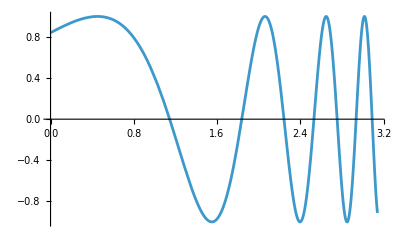

```mathematica
Plot[Sin[Exp[x]], {x, 0, Pi}]
```

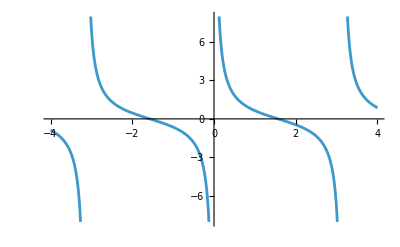

```mathematica
Plot[Cot[x], {x, -4, 4}]
```

```mathematica
(*Plotting Parametric Curves*)
```

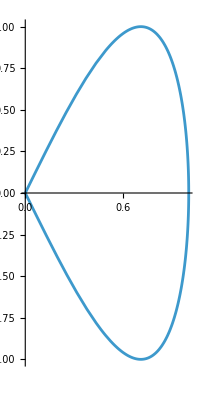

```mathematica
p1 = ParametricPlot[{Sin[t], Sin[2t]}, {t, 0, Pi}]
```

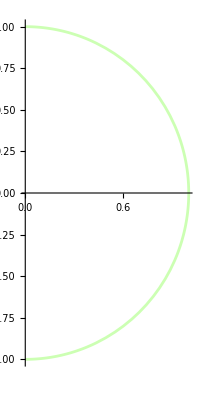

```mathematica
p2 = ParametricPlot[{Sin[t], Cos[t]}, {t, 0, Pi}, PlotStyle->RGBColor[0.8, 1, 0.7]]
```

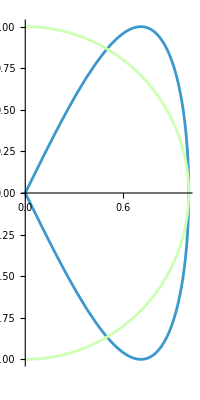

```mathematica
Show[p1, p2]
```

```mathematica
(*Plot a list of points*)
```

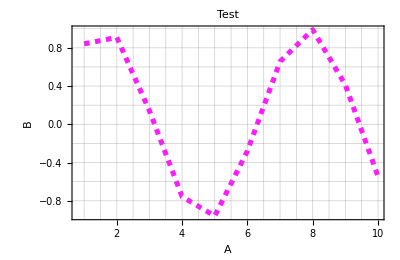

```mathematica
ListPlot[Table[{i, Sin[i]}, {i, 1, 10}], Joined->True, Axes-> False, Frame -> True, PlotStyle-> {RGBColor[1, .1, 1], Thickness[0.0091], Dashing[.01, .04]}, AspectRatio->.65,  PlotLabel->"Test", PlotRange->All, FrameLabel->{A, B}, GridLines->All]
```

```mathematica
(*3D Plot*)
```

```mathematica
Plot3D[Sin[x - y^2], {x, 0, Pi}, {y, -Pi, Pi}]
```

-Graphics3D-

```mathematica
p3 = Plot3D[Sin[x ^2 + y^2], {x, 0, Pi}, {y, 0, Pi}]
```

-Graphics3D-

```mathematica
(*Export plot to image*)
```

```mathematica
Export["fig1.jpg", p3]
```

fig1.jpg

```mathematica
W = Table[Random[], {i, 1, 1000}]
```

{0.154888,0.880228,0.059288,0.952259,0.905289,0.911664,0.518416,0.27557,0.930663,0.328745,0.291515,0.117929,0.0771339,0.606079,0.547979,0.0770904,0.812767,0.708843,0.062958,0.53822,0.769484,0.3125,0.647505,0.938369,0.614596,0.432272,0.588217,0.98611,0.709307,0.520608,0.0698014,0.71054,0.778644,0.191863,0.778286,0.592611,0.70151,0.585784,0.230307,0.515521,0.888744,0.876941,0.167349,0.977301,0.119259,0.56444,0.519843,0.0389323,0.504663,0.132168,0.931626,0.052822,0.795356,0.611559,0.861825,0.342282,0.0167118,0.419696,0.083539,0.749671,0.315202,0.833912,0.853232,0.23415,0.426458,0.956971,0.685884,0.256849,0.307199,0.392531,0.16604,0.217916,0.802535,0.260364,0.234414,0.165094,0.00717953,0.648804,0.372589,0.822813,0.990468,0.229108,0.28905,0.0731418,0.675266,0.395196,0.435818,0.838992,0.248808,0.438225,0.749934,0.582143,0.94161,0.0456938,0.583893,0.364227,0.139074,0.78533,0.349479,0.199133,0.131895,0.136526,0.97689,0.37632,0.141427,0.907418,0.68784,0.303178,0.466161,0.512221,0.252022,0.464186,0.217353,0.0739963,0.502088,0.882043,0.275743,0.0283025,0.918195,0.517816,0.136669,0.242972,0.568716,0.318684,0.00477373,0.106446,0.591825,0.942364,0.863347,0.199028,0.903985,0.639185,0.397186,0.686807,0.651963,0.174999,0.179833,0.61281,0.149874,0.292956,0.904091,0.584508,0.231679,0.77514,0.767422,0.341536,0.662964,0.456456,0.762648,0.23509,0.0711385,0.514093,0.899302,0.0360616,0.167153,0.874907,0.502116,0.349255,0.515191,0.699908,0.322282,0.736445,0.365316,0.406952,0.418192,0.151937,0.133637,0.631812,0.65077,0.810401,0.470673,0.175356,0.888122,0.575311,0.399535,0.661264,0.98882,0.539249,0.232382,0.786356,0.486704,0.189995,0.717191,0.0864481,0.164422,0.45355,0.351875,0.679496,0.74623,0.301613,0.218237,0.0476835,0.0954604,0.491213,0.747564,0.872327,0.207339,0.915901,0.348029,0.211064,0.218519,0.376652,0.115647,0.424708,0.731814,0.186657,0.398456,0.33826,0.567392,0.733107,0.0465819,0.658764,0.821162,0.431494,0.828344,0.61108,0.725702,0.940281,0.0807804,0.738753,0.518363,0.0243799,0.732751,0.527689,0.299844,0.647728,0.617104,0.102981,0.56803,0.461071,0.218647,0.764722,0.000637127,0.727963,0.172066,0.105958,0.179475,0.29647,0.343721,0.494878,0.453773,0.356188,0.262941,0.756125,0.93541,0.331808,0.530189,0.228436,0.635566,0.68408,0.913085,0.125455,0.0675365,0.22301,0.694438,0.360733,0.0668994,0.495046,0.522372,0.254775,0.887424,0.198577,0.178651,0.759898,0.433651,0.842388,0.915711,0.00377243,0.498241,0.51058,0.385521,0.775336,0.862675,0.8265,0.472436,0.649881,0.795139,0.60349,0.777998,0.289148,0.728239,0.108444,0.255625,0.0343721,0.840815,0.909868,0.076974,0.274475,0.407163,0.0674794,0.161263,0.270702,0.908922,0.556899,0.775742,0.495366,0.0462471,0.7304,0.303306,0.845485,0.251109,0.126909,0.525309,0.556337,0.522869,0.0184653,0.269683,0.521965,0.682055,0.108598,0.192709,0.247491,0.274891,0.0411182,0.031446,0.976789,0.365969,0.484219,0.255704,0.481423,0.319722,0.753819,0.952397,0.635938,0.0686137,0.62691,0.427089,0.0796003,0.545744,0.608445,0.157405,0.557635,0.86369,0.499847,0.964696,0.310144,0.588798,0.458729,0.93325,0.333355,0.222829,0.97451,0.677546,0.851933,0.903107,0.220691,0.725149,0.215995,0.834493,0.593781,0.29806,0.136395,0.288749,0.985336,0.140655,0.57876,0.425059,0.485489,0.175959,0.268615,0.836261,0.0267608,0.242709,0.93526,0.613432,0.052251,0.565163,0.0833272,0.710325,0.83156,0.840014,0.867332,0.875832,0.237779,0.541954,0.730938,0.587083,0.252443,0.4013,0.152178,0.162024,0.766954,0.225341,0.883562,0.325763,0.740193,0.982632,0.948302,0.712331,0.687942,0.41747,0.864975,0.00200557,0.856382,0.577456,0.997643,0.126174,0.618602,0.0355013,0.266705,0.539091,0.366159,0.634202,0.114527,0.377067,0.599205,0.408861,0.230965,0.0513048,0.859012,0.426228,0.282663,0.338974,0.171071,0.00875855,0.417688,0.336969,0.314689,0.431303,0.420045,0.210795,0.696087,0.395802,0.153339,0.671704,0.329928,0.7616,0.0388119,0.294637,0.730723,0.352739,0.807847,0.243332,0.87171,0.926511,0.525184,0.904358,0.70064,0.917753,0.107496,0.567389,0.385951,0.48645,0.687452,0.356594,0.689864,0.0906481,0.534112,0.68489,0.359936,0.329048,0.4953,0.390254,0.629213,0.976309,0.687453,0.146922,0.757503,0.0497972,0.162269,0.242564,0.0568631,0.132044,0.0547729,0.675175,0.670912,0.645595,0.367321,0.318581,0.981048,0.554947,0.833209,0.633691,0.621113,0.225899,0.337909,0.243437,0.991899,0.24959,0.650455,0.0965155,0.234396,0.199793,0.488186,0.853951,0.177533,0.0677484,0.433413,0.178776,0.506621,0.422154,0.0660917,0.860195,0.525573,0.867207,0.232883,0.226504,0.90446,0.641308,0.894974,0.983067,0.912561,0.391718,0.244519,0.886551,0.678164,0.191925,0.756333,0.0326,0.500631,0.124177,0.32292,0.853824,0.99401,0.702023,0.256828,0.993629,0.468438,0.834816,0.0239456,0.767125,0.563978,0.193508,0.128972,0.784058,0.651417,0.80179,0.884453,0.897507,0.973253,0.609865,0.12812,0.864907,0.472622,0.485688,0.8052,0.011083,0.478612,0.783664,0.548372,0.017454,0.0101741,0.948848,0.524426,0.250329,0.446197,0.75534,0.395455,0.466271,0.79478,0.95355,0.511002,0.568764,0.821527,0.343685,0.382882,0.703857,0.348905,0.857998,0.577681,0.692774,0.870294,0.0743333,0.0293094,0.67532,0.86012,0.125486,0.504883,0.424991,0.413923,0.370146,0.109428,0.95872,0.619143,0.416596,0.598426,0.389956,0.797616,0.072911,0.215545,0.686099,0.448711,0.214913,0.637863,0.993326,0.578417,0.14058,0.608554,0.318006,0.718297,0.0150946,0.103671,0.893015,0.304374,0.644949,0.994243,0.934295,0.685231,0.228353,0.395816,0.544339,0.887614,0.155442,0.180272,0.858239,0.438904,0.940528,0.542409,0.864913,0.860487,0.799948,0.933855,0.546908,0.14219,0.784853,0.830184,0.653893,0.837816,0.139905,0.835942,0.719598,0.152585,0.911552,0.440125,0.175259,0.26497,0.756111,0.259853,0.31702,0.826067,0.815582,0.717444,0.452106,0.96558,0.0156344,0.783589,0.905199,0.82339,0.230781,0.953405,0.251306,0.985575,0.0908761,0.117463,0.531709,0.83299,0.179324,0.677338,0.35645,0.568019,0.423213,0.417485,0.0394299,0.741952,0.607631,0.70004,0.587324,0.776373,0.591996,0.916451,0.682125,0.952982,0.361215,0.963046,0.430819,0.967408,0.270339,0.845583,0.89911,0.134418,0.0910155,0.168245,0.542661,0.566399,0.667802,0.750761,0.503231,0.824446,0.0601714,0.0507205,0.915907,0.0480735,0.468175,0.13427,0.233782,0.0950913,0.10696,0.171223,0.802963,0.127684,0.83662,0.32564,0.903853,0.993266,0.745605,0.157395,0.361192,0.426867,0.0778025,0.406635,0.857961,0.602421,0.0176311,0.355914,0.942054,0.554348,0.549456,0.221645,0.708272,0.459257,0.442497,0.0504213,0.905309,0.331573,0.605876,0.724781,0.00145595,0.338307,0.860272,0.567385,0.640264,0.911439,0.782469,0.160751,0.782303,0.309018,0.764838,0.804836,0.840249,0.75467,0.215382,0.583192,0.131977,0.295414,0.772885,0.53277,0.226668,0.963841,0.167009,0.80799,0.225212,0.625534,0.306737,0.240604,0.584948,0.714095,0.524268,0.0798534,0.802646,0.405077,0.75943,0.275017,0.962397,0.650406,0.544048,0.691825,0.83042,0.354993,0.771162,0.159055,0.603752,0.391152,0.604153,0.351065,0.378539,0.765618,0.297416,0.110461,0.793591,0.0515233,0.773148,0.0306076,0.990945,0.646447,0.0137183,0.755591,0.0285488,0.99604,0.469671,0.0637654,0.198129,0.641048,0.698508,0.904711,0.594377,0.249896,0.0943547,0.553645,0.215838,0.484278,0.796938,0.443184,0.422247,0.432755,0.0237903,0.412577,0.431302,0.786308,0.0100719,0.656986,0.402753,0.790268,0.540401,0.593221,0.204624,0.14922,0.841893,0.68851,0.610247,0.899324,0.747539,0.134865,0.394408,0.415046,0.9506,0.69168,0.972161,0.982291,0.92681,0.279103,0.54086,0.195983,0.916738,0.622117,0.138107,0.405715,0.376337,0.0288964,0.933483,0.256496,0.534443,0.340386,0.323236,0.357172,0.786905,0.205522,0.928828,0.942126,0.836304,0.513841,0.956667,0.959835,0.909495,0.234738,0.415807,0.763852,0.992757,0.612621,0.2777,0.358136,0.61642,0.583725,0.344217,0.101641,0.0819767,0.243338,0.0209806,0.744469,0.295072,0.0378166,0.0921526,0.802343,0.458768,0.523975,0.135486,0.842509,0.549273,0.289237,0.719679,0.0786568,0.556516,0.676616,0.441979,0.72052,0.940096,0.0928917,0.097762,0.618879,0.85812,0.849554,0.0767814,0.87441,0.563048,0.811737,0.984629,0.0720669,0.10428,0.287762,0.849143,0.229558,0.555007,0.998525,0.129464,0.150901,0.998491,0.321908,0.687485,0.430381,0.0583941,0.229017,0.589723,0.811502,0.200274,0.379463,0.512941,0.937091,0.637227,0.567726,0.528313,0.865024,0.532947,0.279964,0.67917,0.635466,0.977939,0.28144,0.549706,0.484565,0.979449,0.959532,0.862221,0.0541836,0.921055,0.730515,0.272499,0.242682,0.72078,0.351052,0.759557,0.305591,0.0835538,0.783326,0.231244,0.440566,0.550607,0.503362,0.552074,0.8051,0.572668,0.221922,0.00236839,0.320535,0.593219,0.26239,0.140147,0.266352,0.672164,0.531875,0.867649,0.0236696,0.951384,0.180823,0.108091,0.718079,0.86783,0.397496,0.876847,0.277513,0.317223,0.894135,0.324773,0.472413,0.744555,0.672213,0.322404,0.151878,0.151336,0.409823,0.182257,0.885526,0.479172,0.877948,0.314609,0.861856,0.527788,0.697126,0.206517,0.143778,0.659958,0.29963,0.32967,0.866265,0.342735,0.405495,0.0048975,0.393852,0.59818,0.733282,0.682493,0.241974,0.446844,0.323458,0.500236,0.356448,0.967673,0.44551,0.185628,0.494592,0.439885,0.748384}

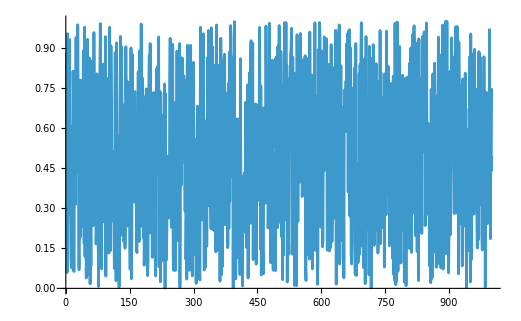

```mathematica
ListPlot[Table[{i, Transpose[W][[i]]}, {i, 1, 1000}], Joined->True]
```